### DIY Lecture 21 - S Tarun Prasad - ME17B114

### ( 1 )

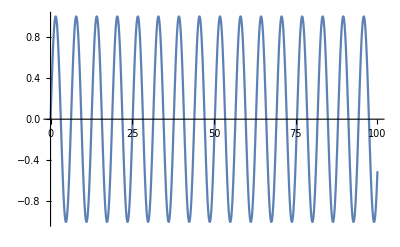

```mathematica
Plot[Evaluate[θ[t]/.NDSolve[{θ''[t]+θ[t]==0,θ'[0] == 1,θ[0] ==0},θ,{t,0,100}]],{t,0,100}]
```

### (2)

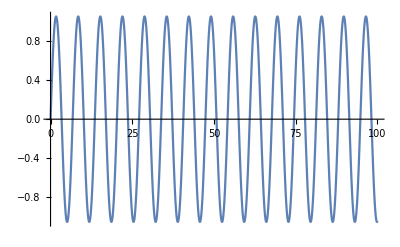

```mathematica
Plot[Evaluate[θ[t]/.NDSolve[{θ''[t]+(θ[t]-(θ[t]^3/6))== 0,θ'[0] == 1,θ[0] ==0},θ,{t,0,100}]],{t,0,100}]
```

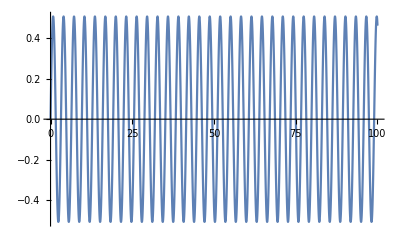

```mathematica
Plot[Evaluate[θ[t]/.NDSolve[{θ''[t]+4*(θ[t]-(θ[t]^3/6))== 0,θ'[0] == 1,θ[0] ==0},θ,{t,0,100}]],{t,0,100}]
```

As seen in the above 2 graphs for ω0^2 = 1 and ω0^2 = 4, only the frequencies change. The nature of the graph as such is the same.